```mathematica
SetDirectory[NotebookDirectory[]];
Get["dlNdlxEW.m"]
```

-0.01

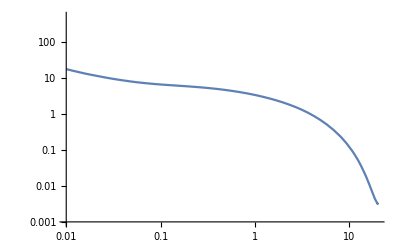

```mathematica
LogLogPlot[10^(dlNdlxIEW["τ"->"γ"][20,Log[10,x/20]])*Log[10]/(x),{x,.01,20.},PlotRange->{Automatic,{.001,500}}]
```

```mathematica
dlNdlxIEW["V→e"->"e"][20,Log[10,0.1]]
```

-0.295582

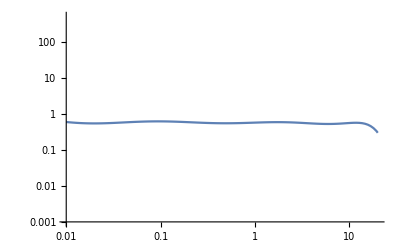

```mathematica
LogLogPlot[10^(dlNdlxIEW["V→e"->"e"][20,Log[10,x/20]])*Log[10]/(x),{x,.01,20.},PlotRange->{Automatic,{.001,1000}}]
```

```mathematica
dlNdlxIEW["b"->"γ"][20,Log[10,.01]]/(.01*20)
```

6.10755

```mathematica
filename5 = Table[StringJoin["spectra/unbinned/bbar/muomega-gammayield-",ToString[j],".dat"],{j,1,140}];
```

```mathematica
m5 = Table[20.+i*.5,{i,1,140}];
```

```mathematica
Export["spectra/unbinned/bbar/bbar_mass_table.txt",Table[{k,m5[[k]]},{k,1,140}],"Table"]
```

spectra/unbinned/bbar/bbar_mass_table.txt

```mathematica
For[j=1,j<141,j++,Export[filename5[[j]],Table[{.01*i,.19*10^(dlNdlxIEW["b"->"γ"][m5[[j]],Log[10,.01*i/m5[[j]]]])*Log[10]/(.01*i)},{i,100*m5[[j]]}]]]
```

```mathematica
filename6 = Table[StringJoin["spectra/unbinned/tau/muomega-gammayield-",ToString[j],".dat"],{j,1,140}];
```

```mathematica
m6 = Table[5.+i*.5,{i,1,140}];
```

```mathematica
Export["spectra/unbinned/tau/tau_mass_table.txt",Table[{k,m6[[k]]},{k,1,140}],"Table"]
```

spectra/unbinned/tau/tau_mass_table.txt

```mathematica
For[j=1,j<141,j++,Export[filename6[[j]],Table[{.01*i,.19*10^(dlNdlxIEW["τ"->"γ"][m6[[j]],Log[10,.01*i/m6[[j]]]])*Log[10]/(.01*i)},{i,100*m6[[j]]}]]]
```